# Notebook 06: Curves

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## The BezierCurve command

There are a couple of different ways to draw curved lines with the Graphics command. One is to use the BezierCurve command.

To specify a Bézier curve, you need to include both points on the line and control points. Here is a specification for a curve that opens upward. The points {0, 0} and {3, 0} are endpoints on the curve, drawn in red. The other two points are control points, drawn in blue. Note that the control points do not lie on the curve.

```mathematica
concaveUp={{0,0},{1,-1},{2,-1},{3,0}};
```

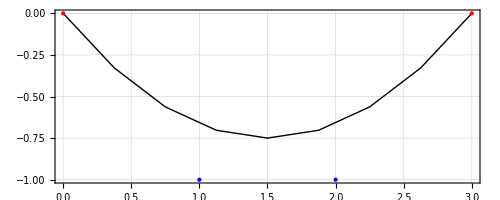

```mathematica
Graphics[{BezierCurve[concaveUp],PointSize[Medium],Red,Point[{{0,0},{3,0}}],Blue,Point[{{1,-1},{2,-1}}]},Frame->True,GridLines->Automatic]
```

If we move both control points down, the curve becomes deeper.

```mathematica
concaveUpDeeper={{0,0},{1,-3},{2,-3},{3,0}};
```

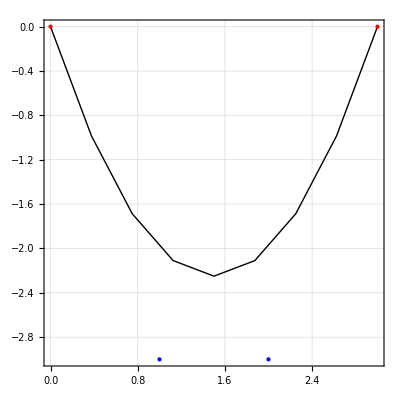

```mathematica
Graphics[{BezierCurve[concaveUpDeeper],PointSize[Medium],Red,Point[{{0,0},{3,0}}],Blue,Point[{{1,-3},{2,-3}}]},Frame->True,GridLines->Automatic]
```

If we move the control points closer to the endpoints, the curve becomes broader.

```mathematica
concaveUpBroader={{0,0},{.25,-3},{2.75,-3},{3,0}};
```

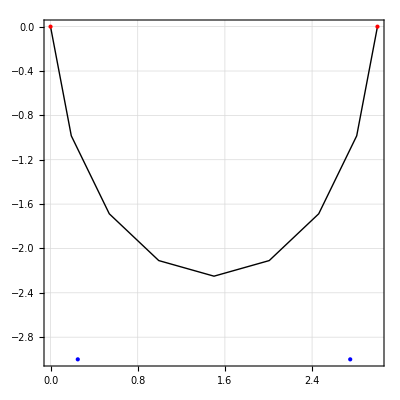

```mathematica
Graphics[{BezierCurve[concaveUpBroader],PointSize[Medium],Red,Point[{{0,0},{3,0}}],Blue,Point[{{.25,-3},{2.75,-3}}]},Frame->True,GridLines->Automatic]
```

If the control points are above the line, we end up with a curve that opens downward.

```mathematica
concaveDown={{0,0},{1,1},{2,1},{3,0}};
```

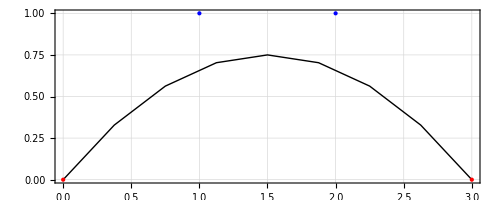

```mathematica
Graphics[{BezierCurve[concaveDown],PointSize[Medium],Red,Point[{{0,0},{3,0}}],Blue,Point[{{1,1},{2,1}}]},Frame->True,GridLines->Automatic]
```

It helps to visualize what the control points are doing to the curve if we plot a line through them. Here the line through the control points is drawn in purple.

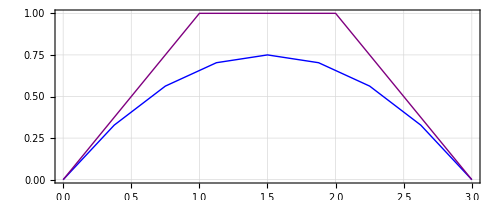

```mathematica
Graphics[{Blue,BezierCurve[concaveDown],Purple,Line[concaveDown]},Frame->True,GridLines->Automatic]
```

If we place one control point above the line and one below it, we can get an S-shape. All points are shown in Red in the following figure.

```mathematica
sShape={{0,0},{1,-1},{2,1},{3,0}};
```

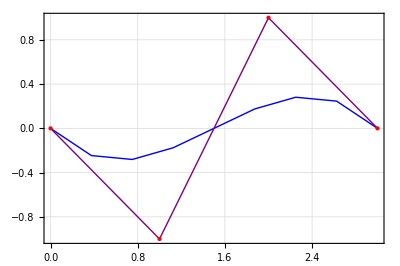

```mathematica
Graphics[{Blue,BezierCurve[sShape],Purple,Line[sShape],PointSize[Medium],Red,Point[sShape]},Frame->True,GridLines->Automatic]
```

If you have ever used the ink pen tool in a vector graphics program like Adobe Illustrator, you were drawing with Bézier curves.

## Composite and closed Bézier curves

### Composite curves

We can join multiple curves together by using a longer list of points. The first point is on the curve, the next two are control points, the fourth point is on the curve, the next two are control points, the seventh point is on the curve, and so on. The image below shows a composite curve in blue and a purple line through its control points.

```mathematica
compositeCurve={{0,0},{1,1},{2,-1},{3,0},{5,2},{6,-1},{7,3}};
```

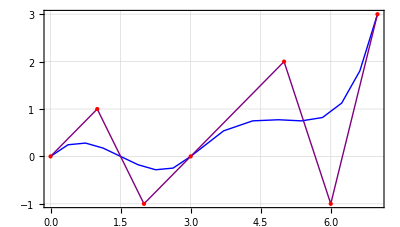

```mathematica
Graphics[{Blue,BezierCurve[compositeCurve],Purple,Line[compositeCurve],PointSize[Medium],Red,Point[compositeCurve]},Frame->True,GridLines->Automatic]
```

If the control points to the left and right of a point that lies on a composite line are both on the same side, the curve comes to a sharp point. Look at the point at {3, 0} in the following image.

```mathematica
sharpAngle={{0,0},{1,1},{2,1},{3,0},{4,1},{5,0},{6,1}};
```

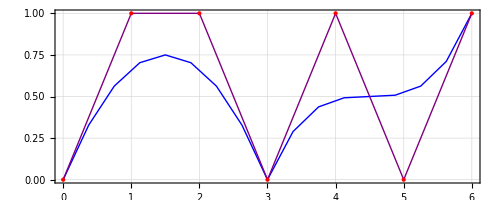

```mathematica
Graphics[{Blue,BezierCurve[sharpAngle],Purple,Line[sharpAngle],PointSize[Medium],Red,Point[sharpAngle]},Frame->True,GridLines->Automatic]
```

### Closed curves

By default, the last point on a Bézier curve is not connected to the first one. You can change this behaviour by setting the SplineClosed attribute to true. This allows you to draw closed figures like the one shown below.

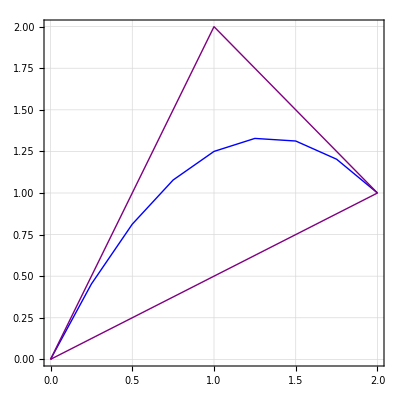

```mathematica
Graphics[{Blue,BezierCurve[{{0,0},{1,2},{2,1}},SplineClosed->True],Purple,Line[{{0,0},{1,2},{2,1},{0,0}}]},Frame->True,GridLines->Automatic]
```

## Thickness and dashing

The Thickness command allows us to specify line thickness. Note how Table is used here to create a list of images.

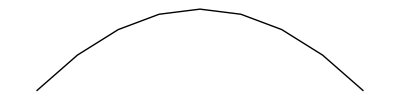
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{Thickness[i],BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{Tiny,Small,Medium,Large}}]
```

A different version of Thickness allows us to specify what proportion of the overall image the thickness of the line should take up.

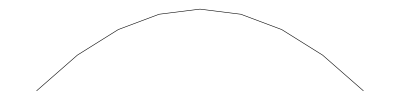
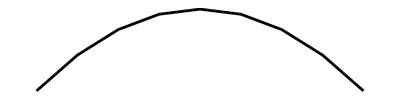
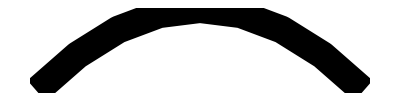
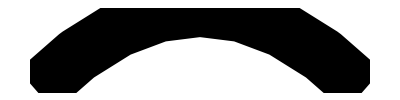

```mathematica
Table[Graphics[{Thickness[i],BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{.001,.005,.05,.1}}]
```

We have seen that we can specify different kinds of lines with commands like Dotted and Dashed.

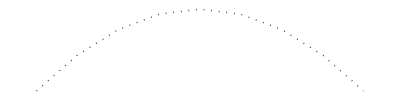
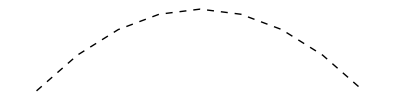
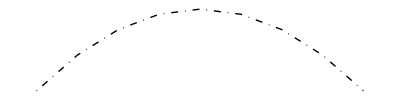
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{i,BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{Dotted,Dashed,DotDashed,Dashing[None]}}]
```

The Dashing command allows us to specify scaled lengths for the line segments and spaces between them.

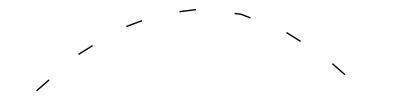
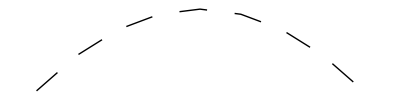
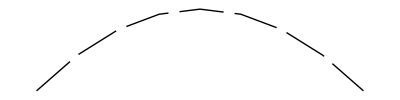
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[{Dashing[{i,0.1-i}],BezierCurve[{{0,0},{1,1},{2,1},{3,0}}]}],{i,{.01,.03,.05,.08}}]
```

## Edges and faces

We can specify the style of the edges and filling of polygons and other graphic objects with EdgeForm and FaceForm. The Darker command makes a colour darker.

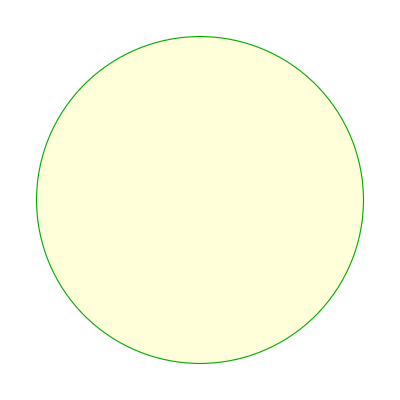

```mathematica
Graphics[{EdgeForm[{Thick,Darker[Green]}],FaceForm[LightYellow],Disk[]}]
```

The CapForm command determines the shape of the ends of lines.

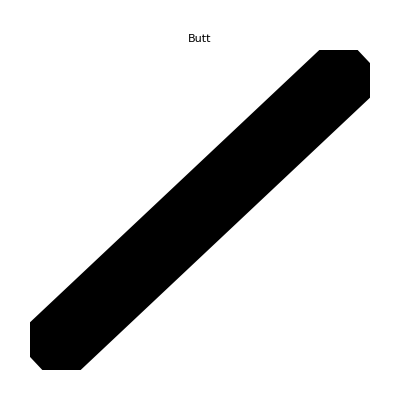
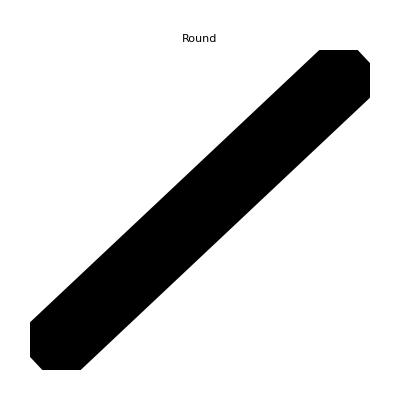
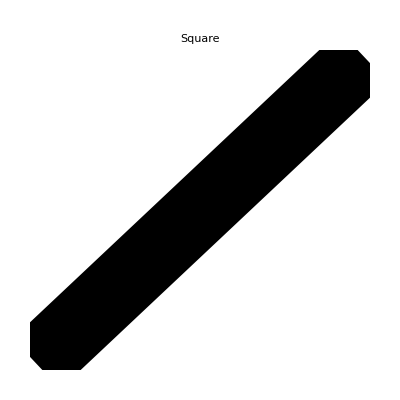

```mathematica
Table[Graphics[{CapForm[cap],Thickness[.2],Line[{{-1,-1},{1,1}}]},PlotLabel->cap,ImagePadding->20],{cap,{"Butt","Round","Square"}}]
```

The JoinForm command determines the shape when lines meet.

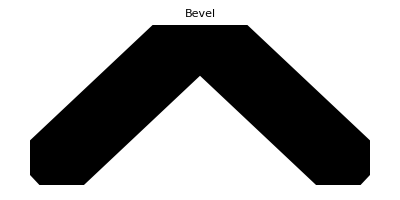
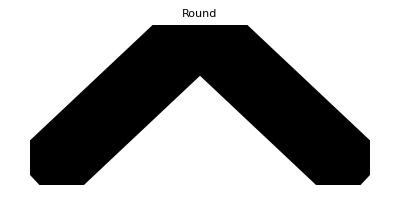
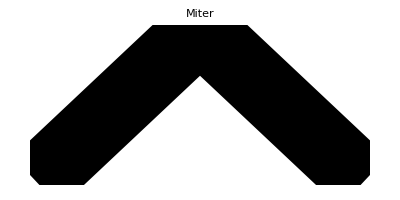

```mathematica
Table[Graphics[{JoinForm[j],Thickness[.2],Line[{{-1,-0.5},{0,0.5},{1,-0.5}}]},PlotLabel->j,ImagePadding->20],{j,{"Bevel","Round","Miter"}}]
```

## Tables of Curves

We can ‘morph’ between a straight line and a curve by using Table to plot a series of intermediate curves. We need to use PlotRange here to focus on the figure, because otherwise Graphics includes space for the control points, even though they aren’t being plotted.

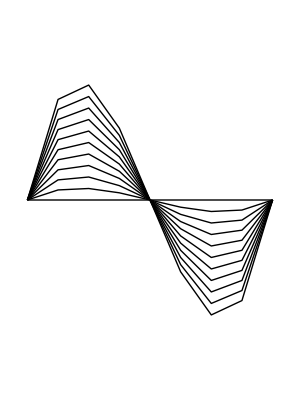

```mathematica
Graphics[Table[BezierCurve[{{0,0},{1,u},{2,-u},{3,0}}],{u,0,5,.5}],PlotRange->{-2,2}]
```

Here is what the above figure looks like if we plot all the control points, too.

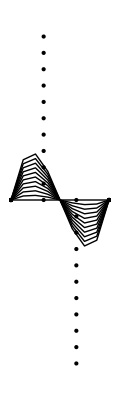

```mathematica
Graphics[{Table[{BezierCurve[{{0,0},{1,u},{2,-u},{3,0}}],Point[{{0,0},{1,u},{2,-u},{3,0}}]},{u,0,5,.5}]}]
```

We can make flower- and pinwheel-like shapes by rotating closed Bézier curves.

```mathematica
Graphics[Table[Rotate[BezierCurve[{{0,0},{1,2},{2,0}},SplineClosed->True],r Degree],{r,0,315,45}]]
```

-Graphics-

```mathematica
Graphics[Table[Rotate[BezierCurve[{{0,0},{1,2},{1,3},{1.5,1}},SplineClosed->True],r Degree],{r,0,360,24}]]
```

-Graphics-

Altering line thickness and opacity can produce interesting results. Note the use of the ImagePadding attribute here.

```mathematica
Graphics[{Pink,Thickness[.1],Opacity[.2],Table[Rotate[BezierCurve[{{0,0},{0,2},{2,0}},SplineClosed->True],r Degree],{r,0,315,45}]},ImagePadding->22]
```

-Graphics-

```mathematica
Graphics[{Blue,Thickness[.02],Opacity[.15],JoinForm["Round"],Table[Rotate[BezierCurve[{{0,0},{0,2},{-1,0}},SplineClosed->True],r Degree],{r,0,345,15}]}]
```

-Graphics-

## In-Class Activity

### Draw a picture using the Graphics command. Use the BezierCurve command to include some curved lines.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course